```mathematica
Clear[nodeCount,all4]
```

```mathematica
nodeCount=8;
```

```mathematica
all4=KSetPartitions[nodeCount,4];Length[all4]
```

1701

```mathematica
patterns={{{1,3},{2},{4},{5}},
{{1},{2,4},{3},{5}},
{{1},{2},{3,5},{4}},
{{1,4},{2},{3},{5}},
{{1},{2,5},{3},{4}}};
patterns
```

{{{1,3},{2},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2},{3,5},{4}},{{1,4},{2},{3},{5}},{{1},{2,5},{3},{4}}}

```mathematica
badpatterns={{{1,3},{2,4},{5}},
{{1,3},{2,5},{4}},
{{1},{2,4},{3,5}},
{{1,4},{2},{3,5}},
{{1,4},{2,5},{3}}}
```

{{{1,3},{2,4},{5}},{{1,3},{2,5},{4}},{{1},{2,4},{3,5}},{{1,4},{2},{3,5}},{{1,4},{2,5},{3}}}

```mathematica
good[k_]:=Select[all4,PartitionHasPattern[#,patterns[[k]]]&];
```

```mathematica
bad[k_]:=Select[all4,PartitionHasPattern[#,badpatterns[[k]]]&];
```

```mathematica
Table[Intersection[good[1],bad[k]],{k,1,5}]
```

{{},{},{},{},{}}

```mathematica
TableForm[Table[Map[SymbolToLabel[SetsToSymbol[#]]&,good[k]],{k,1,5}],TableDirections->Row,TableHeadings->{Map[SymbolToLabel[SetsToSymbol[#]]&,patterns], None}]
```

13♁2♁4♁5 | 1♁24♁3♁5 | 1♁2♁35♁4 | 14♁2♁3♁5 | 1♁25♁3♁4
13♁2♁4♁5678 | 1♁24♁3♁5678 | 1♁2♁35678♁4 | 14♁2♁3♁5678 | 1♁25678♁3♁4
13♁2♁4678♁5 | 1♁24678♁3♁5 | 1♁2♁35♁4678 | 14678♁2♁3♁5 | 1♁25♁3♁4678
13♁2♁478♁56 | 1♁2478♁3♁56 | 1♁2♁356♁478 | 1478♁2♁3♁56 | 1♁256♁3♁478
13♁2♁46♁578 | 1♁246♁3♁578 | 1♁2♁3578♁46 | 146♁2♁3♁578 | 1♁2578♁3♁46
13♁2♁48♁567 | 1♁248♁3♁567 | 1♁2♁3567♁48 | 148♁2♁3♁567 | 1♁2567♁3♁48
13♁2♁467♁58 | 1♁2467♁3♁58 | 1♁2♁358♁467 | 1467♁2♁3♁58 | 1♁258♁3♁467
13♁2♁47♁568 | 1♁247♁3♁568 | 1♁2♁3568♁47 | 147♁2♁3♁568 | 1♁2568♁3♁47
13♁2♁468♁57 | 1♁2468♁3♁57 | 1♁2♁357♁468 | 1468♁2♁3♁57 | 1♁257♁3♁468
13678♁2♁4♁5 | 1♁24♁3678♁5 | 1♁2678♁35♁4 | 14♁2♁3678♁5 | 1♁25♁3678♁4
1378♁2♁4♁56 | 1♁24♁378♁56 | 1♁278♁356♁4 | 14♁2♁378♁56 | 1♁256♁378♁4
136♁2♁4♁578 | 1♁24♁36♁578 | 1♁26♁3578♁4 | 14♁2♁36♁578 | 1♁2578♁36♁4
138♁2♁4♁567 | 1♁24♁38♁567 | 1♁28♁3567♁4 | 14♁2♁38♁567 | 1♁2567♁38♁4
1367♁2♁4♁58 | 1♁24♁367♁58 | 1♁267♁358♁4 | 14♁2♁367♁58 | 1♁258♁367♁4
137♁2♁4♁568 | 1♁24♁37♁568 | 1♁27♁3568♁4 | 14♁2♁37♁568 | 1♁2568♁37♁4
1368♁2♁4♁57 | 1♁24♁368♁57 | 1♁268♁357♁4 | 14♁2♁368♁57 | 1♁257♁368♁4
1378♁2♁46♁5 | 1♁246♁378♁5 | 1♁278♁35♁46 | 146♁2♁378♁5 | 1♁25♁378♁46
136♁2♁478♁5 | 1♁2478♁36♁5 | 1♁26♁35♁478 | 1478♁2♁36♁5 | 1♁25♁36♁478
138♁2♁467♁5 | 1♁2467♁38♁5 | 1♁28♁35♁467 | 1467♁2♁38♁5 | 1♁25♁38♁467
1367♁2♁48♁5 | 1♁248♁367♁5 | 1♁267♁35♁48 | 148♁2♁367♁5 | 1♁25♁367♁48
137♁2♁468♁5 | 1♁2468♁37♁5 | 1♁27♁35♁468 | 1468♁2♁37♁5 | 1♁25♁37♁468
1368♁2♁47♁5 | 1♁247♁368♁5 | 1♁268♁35♁47 | 147♁2♁368♁5 | 1♁25♁368♁47
138♁2♁47♁56 | 1♁247♁38♁56 | 1♁28♁356♁47 | 147♁2♁38♁56 | 1♁256♁38♁47
137♁2♁48♁56 | 1♁248♁37♁56 | 1♁27♁356♁48 | 148♁2♁37♁56 | 1♁256♁37♁48
138♁2♁46♁57 | 1♁246♁38♁57 | 1♁28♁357♁46 | 146♁2♁38♁57 | 1♁257♁38♁46
136♁2♁48♁57 | 1♁248♁36♁57 | 1♁26♁357♁48 | 148♁2♁36♁57 | 1♁257♁36♁48
137♁2♁46♁58 | 1♁246♁37♁58 | 1♁27♁358♁46 | 146♁2♁37♁58 | 1♁258♁37♁46
136♁2♁47♁58 | 1♁247♁36♁58 | 1♁26♁358♁47 | 147♁2♁36♁58 | 1♁258♁36♁47
13♁2678♁4♁5 | 1678♁24♁3♁5 | 1678♁2♁35♁4 | 14♁2678♁3♁5 | 1678♁25♁3♁4
13♁278♁4♁56 | 178♁24♁3♁56 | 178♁2♁356♁4 | 14♁278♁3♁56 | 178♁256♁3♁4
13♁26♁4♁578 | 16♁24♁3♁578 | 16♁2♁3578♁4 | 14♁26♁3♁578 | 16♁2578♁3♁4
13♁28♁4♁567 | 18♁24♁3♁567 | 18♁2♁3567♁4 | 14♁28♁3♁567 | 18♁2567♁3♁4
13♁267♁4♁58 | 167♁24♁3♁58 | 167♁2♁358♁4 | 14♁267♁3♁58 | 167♁258♁3♁4
13♁27♁4♁568 | 17♁24♁3♁568 | 17♁2♁3568♁4 | 14♁27♁3♁568 | 17♁2568♁3♁4
13♁268♁4♁57 | 168♁24♁3♁57 | 168♁2♁357♁4 | 14♁268♁3♁57 | 168♁257♁3♁4
13♁278♁46♁5 | 178♁246♁3♁5 | 178♁2♁35♁46 | 146♁278♁3♁5 | 178♁25♁3♁46
13♁26♁478♁5 | 16♁2478♁3♁5 | 16♁2♁35♁478 | 1478♁26♁3♁5 | 16♁25♁3♁478
13♁28♁467♁5 | 18♁2467♁3♁5 | 18♁2♁35♁467 | 1467♁28♁3♁5 | 18♁25♁3♁467
13♁267♁48♁5 | 167♁248♁3♁5 | 167♁2♁35♁48 | 148♁267♁3♁5 | 167♁25♁3♁48
13♁27♁468♁5 | 17♁2468♁3♁5 | 17♁2♁35♁468 | 1468♁27♁3♁5 | 17♁25♁3♁468
13♁268♁47♁5 | 168♁247♁3♁5 | 168♁2♁35♁47 | 147♁268♁3♁5 | 168♁25♁3♁47
13♁28♁47♁56 | 18♁247♁3♁56 | 18♁2♁356♁47 | 147♁28♁3♁56 | 18♁256♁3♁47
13♁27♁48♁56 | 17♁248♁3♁56 | 17♁2♁356♁48 | 148♁27♁3♁56 | 17♁256♁3♁48
13♁28♁46♁57 | 18♁246♁3♁57 | 18♁2♁357♁46 | 146♁28♁3♁57 | 18♁257♁3♁46
13♁26♁48♁57 | 16♁248♁3♁57 | 16♁2♁357♁48 | 148♁26♁3♁57 | 16♁257♁3♁48
13♁27♁46♁58 | 17♁246♁3♁58 | 17♁2♁358♁46 | 146♁27♁3♁58 | 17♁258♁3♁46
13♁26♁47♁58 | 16♁247♁3♁58 | 16♁2♁358♁47 | 147♁26♁3♁58 | 16♁258♁3♁47
136♁278♁4♁5 | 178♁24♁36♁5 | 178♁26♁35♁4 | 14♁278♁36♁5 | 178♁25♁36♁4
1378♁26♁4♁5 | 16♁24♁378♁5 | 16♁278♁35♁4 | 14♁26♁378♁5 | 16♁25♁378♁4
1367♁28♁4♁5 | 18♁24♁367♁5 | 18♁267♁35♁4 | 14♁28♁367♁5 | 18♁25♁367♁4
138♁267♁4♁5 | 167♁24♁38♁5 | 167♁28♁35♁4 | 14♁267♁38♁5 | 167♁25♁38♁4
1368♁27♁4♁5 | 17♁24♁368♁5 | 17♁268♁35♁4 | 14♁27♁368♁5 | 17♁25♁368♁4
137♁268♁4♁5 | 168♁24♁37♁5 | 168♁27♁35♁4 | 14♁268♁37♁5 | 168♁25♁37♁4
137♁28♁4♁56 | 18♁24♁37♁56 | 18♁27♁356♁4 | 14♁28♁37♁56 | 18♁256♁37♁4
138♁27♁4♁56 | 17♁24♁38♁56 | 17♁28♁356♁4 | 14♁27♁38♁56 | 17♁256♁38♁4
136♁28♁4♁57 | 18♁24♁36♁57 | 18♁26♁357♁4 | 14♁28♁36♁57 | 18♁257♁36♁4
138♁26♁4♁57 | 16♁24♁38♁57 | 16♁28♁357♁4 | 14♁26♁38♁57 | 16♁257♁38♁4
136♁27♁4♁58 | 17♁24♁36♁58 | 17♁26♁358♁4 | 14♁27♁36♁58 | 17♁258♁36♁4
137♁26♁4♁58 | 16♁24♁37♁58 | 16♁27♁358♁4 | 14♁26♁37♁58 | 16♁258♁37♁4
137♁28♁46♁5 | 18♁246♁37♁5 | 18♁27♁35♁46 | 146♁28♁37♁5 | 18♁25♁37♁46
138♁27♁46♁5 | 17♁246♁38♁5 | 17♁28♁35♁46 | 146♁27♁38♁5 | 17♁25♁38♁46
136♁28♁47♁5 | 18♁247♁36♁5 | 18♁26♁35♁47 | 147♁28♁36♁5 | 18♁25♁36♁47
138♁26♁47♁5 | 16♁247♁38♁5 | 16♁28♁35♁47 | 147♁26♁38♁5 | 16♁25♁38♁47
136♁27♁48♁5 | 17♁248♁36♁5 | 17♁26♁35♁48 | 148♁27♁36♁5 | 17♁25♁36♁48
137♁26♁48♁5 | 16♁248♁37♁5 | 16♁27♁35♁48 | 148♁26♁37♁5 | 16♁25♁37♁48

```mathematica
16^5
```

1048576

```mathematica
FindFiner[good[1][[1]]]
```

{{{1},{2},{3},{4},{5,6,7}},{{1,3},{2},{4},{5},{6,7}},{{1,3},{2},{4},{5,6},{7}},{{1,3},{2},{4},{5,7},{6}}}

```mathematica
good[1]
```

{{{1,3},{2},{4},{5,6,7}},{{1,3},{2},{4,6,7},{5}},{{1,3},{2},{4,7},{5,6}},{{1,3},{2},{4,6},{5,7}},{{1,3,6,7},{2},{4},{5}},{{1,3,7},{2},{4},{5,6}},{{1,3,6},{2},{4},{5,7}},{{1,3,7},{2},{4,6},{5}},{{1,3,6},{2},{4,7},{5}},{{1,3},{2,6,7},{4},{5}},{{1,3},{2,7},{4},{5,6}},{{1,3},{2,6},{4},{5,7}},{{1,3},{2,7},{4,6},{5}},{{1,3},{2,6},{4,7},{5}},{{1,3,6},{2,7},{4},{5}},{{1,3,7},{2,6},{4},{5}}}

```mathematica
Block[{goodies=Table[good[k],{k,1,5}],pos2, max2,indices,base, finer={},vect,result={}},
base=Length[goodies[[1]]];
Print[base];
max2=base^5;
Print[base,"    ", max2];
Monitor[
For[pos2=0,pos2<max2,pos2++,
indices=PadLeft[IntegerDigits[pos2,base],5]+1;
finer={};
For[vect=1,vect<=5,vect++,
finer=Join[finer,FindFiner[goodies[[vect,indices[[vect]] ]] ]];
];
finer=DeleteDuplicates[finer];
AppendTo[result,Length[finer]]
],
{pos2,N[pos2/max2*100,4]}];
Sort[Tally[result]]
]
```

16

16    1048576

{{13,300},{14,6970},{15,48256},{16,144110},{17,234760},{18,229110},{19,154980},{20,101489},{21,68130},{22,33055},{23,15610},{24,7840},{25,2565},{26,1035},{27,300},{28,55},{29,10},{30,1}}

```mathematica
FindFiner[{{1,3},{2,5},{4},{6,7,8,9,10,11}}]//Length
```

33

```mathematica
Binomial[6,2]+Binomial[2,2]+Binomial[2,2]+Binomial[1,2]
```

17

```mathematica
Block[{goodies=Table[good[k],{k,1,5}], badies=Flatten[Table[bad[k],{k,1,5}],1],pos2, max2,indices,base, finer={}, pos3, currentfine,vect,result={},coarser},
base=Length[goodies[[1]]];
Print[base];
max2=base^5;
max2=10000;
Print[base,"    ", max2,"    ", Length[badies]];
Monitor[
For[pos2=0,pos2<max2,pos2++,
indices=PadLeft[IntegerDigits[pos2,base],5]+1;
finer={};
For[vect=1,vect<=5,vect++,
finer=Join[finer,FindFiner[goodies[[vect,indices[[vect]] ]] ]];
];
finer=DeleteDuplicates[finer];
coarser={};
For[pos3=1,pos3≤Length[finer],pos3++,
currentfine=finer[[pos3]];
coarser=Join[coarser,FindCoarser[currentfine]]
];
coarser=DeleteDuplicates[coarser];
AppendTo[result,{Length[finer],Length[coarser],Length[Intersection[coarser,badies]]}]
],
{pos2,N[pos2/max2*100,4]}];
Sort[Tally[Map[Last,result]]]
]
```

64

64    10000    185

{{35,13},{36,22},{37,58},{38,310},{39,657},{40,838},{41,1376},{42,1080},{43,742},{44,263},{45,181},{46,780},{47,1068},{48,1443},{49,467},{50,318},{53,241},{54,51},{55,84},{59,8}}

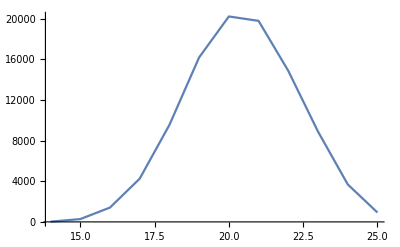

```mathematica
ListLinePlot[{{14,22},{15,277},{16,1410},{17,4253},{18,9539},{19,16179},{20,20205},{21,19771},{22,14854},{23,8882},{24,3688},{25,920}}]
```

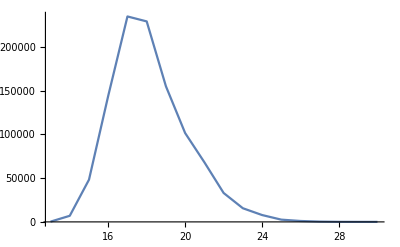

```mathematica
ListLinePlot[{{13,300},{14,6970},{15,48256},{16,144110},{17,234760},{18,229110},{19,154980},{20,101489},{21,68130},{22,33055},{23,15610},{24,7840},{25,2565},{26,1035},{27,300},{28,55},{29,10},{30,1}}]
```

```mathematica
FindCoarser[{{1,3},{2,5},{4},{6,7,8,9,10,11}}]
```

{{{1,2,3,5},{4},{6,7,8,9,10,11}},{{1,3,4},{2,5},{6,7,8,9,10,11}},{{1,3,6,7,8,9,10,11},{2,5},{4}},{{1,3},{2,4,5},{6,7,8,9,10,11}},{{1,3},{2,5,6,7,8,9,10,11},{4}},{{1,3},{2,5},{4,6,7,8,9,10,11}}}

```mathematica
FindCoarser []
```

## nOW WORK from the bad up to find a minimal set of 5

```mathematica
Block[{badies=Flatten[Table[bad[k],{k,1,5}],1], fourFromFive=Association[], fives={},currentFives,vertices,edges},
Table[
currentFives=FindFiner[b];
Table[
If[!KeyExistsQ[fourFromFive,f],
fourFromFive[f]={}
];
fourFromFive[f]=Append[fourFromFive[f],b]
,
{f,currentFives}];
fives=Join[fives,currentFives]

,
{b,badies}
];
vertices={};
edges={};
Table[
AppendTo[vertices,SetsToSymbol[k]];
Table[
AppendTo[vertices,SetsToSymbol[four]];
AppendTo[edges,SetsToSymbol[k]-> SetsToSymbol[four]];
,{four,fourFromFive[k]}
]
,
{k,Keys[fourFromFive]}
];
vertices=DeleteDuplicates[vertices];
Print[Length[DeleteDuplicates[fives]]];
(*Print[Graph[vertices,edges,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
];*)
Sort[Tally[Map[Last,Tally[fives]]]]
]
```

50

{{2,45},{7,5}}

```mathematica
Table[StirlingS2[4,k],{k,1,10}]
```

{1,7,6,1,0,0,0,0,0,0}

```mathematica
Block[{badies=Flatten[Table[bad[k],{k,1,5}],1], fourFromFive=Association[], fives={},currentFives,vertices,edges, whichFives, whichFours, covered},
Table[
currentFives=FindFiner[b];
Table[
If[!KeyExistsQ[fourFromFive,f],
fourFromFive[f]={}
];
fourFromFive[f]=Append[fourFromFive[f],b]
,
{f,currentFives}];
fives=Join[fives,currentFives]

,
{b,badies}
];
whichFives=Map[First,Select[Tally[fives],#[[2]]==7&]];
covered={};
Table[
covered=Join[covered,FindCoarser[five]]
,
{five,whichFives}
];
Print[Length[badies]];
Print[badies];
Print[covered];
Print[SetDifference[badies,covered]];
Sort[Tally[Map[Last,Tally[covered]]]]
]
```

35

{{{1,3},{2,4},{5},{6,7}},{{1,3},{2,4},{5,6},{7}},{{1,3},{2,4},{5,7},{6}},{{1,3},{2,4,6},{5},{7}},{{1,3},{2,4,7},{5},{6}},{{1,3,6},{2,4},{5},{7}},{{1,3,7},{2,4},{5},{6}},{{1,3},{2,5},{4},{6,7}},{{1,3},{2,5,6},{4},{7}},{{1,3},{2,5,7},{4},{6}},{{1,3},{2,5},{4,6},{7}},{{1,3},{2,5},{4,7},{6}},{{1,3,6},{2,5},{4},{7}},{{1,3,7},{2,5},{4},{6}},{{1},{2,4},{3,5},{6,7}},{{1},{2,4},{3,5,6},{7}},{{1},{2,4},{3,5,7},{6}},{{1},{2,4,6},{3,5},{7}},{{1},{2,4,7},{3,5},{6}},{{1,6},{2,4},{3,5},{7}},{{1,7},{2,4},{3,5},{6}},{{1,4},{2},{3,5},{6,7}},{{1,4},{2},{3,5,6},{7}},{{1,4},{2},{3,5,7},{6}},{{1,4,6},{2},{3,5},{7}},{{1,4,7},{2},{3,5},{6}},{{1,4},{2,6},{3,5},{7}},{{1,4},{2,7},{3,5},{6}},{{1,4},{2,5},{3},{6,7}},{{1,4},{2,5,6},{3},{7}},{{1,4},{2,5,7},{3},{6}},{{1,4,6},{2,5},{3},{7}},{{1,4,7},{2,5},{3},{6}},{{1,4},{2,5},{3,6},{7}},{{1,4},{2,5},{3,7},{6}}}

{{{1,2,3,4},{5},{6},{7}},{{1,3,5},{2,4},{6},{7}},{{1,3,6},{2,4},{5},{7}},{{1,3,7},{2,4},{5},{6}},{{1,3},{2,4,5},{6},{7}},{{1,3},{2,4,6},{5},{7}},{{1,3},{2,4,7},{5},{6}},{{1,3},{2,4},{5,6},{7}},{{1,3},{2,4},{5,7},{6}},{{1,3},{2,4},{5},{6,7}},{{1,2,3,5},{4},{6},{7}},{{1,3,4},{2,5},{6},{7}},{{1,3,6},{2,5},{4},{7}},{{1,3,7},{2,5},{4},{6}},{{1,3},{2,4,5},{6},{7}},{{1,3},{2,5,6},{4},{7}},{{1,3},{2,5,7},{4},{6}},{{1,3},{2,5},{4,6},{7}},{{1,3},{2,5},{4,7},{6}},{{1,3},{2,5},{4},{6,7}},{{1,2,4},{3,5},{6},{7}},{{1,3,5},{2,4},{6},{7}},{{1,6},{2,4},{3,5},{7}},{{1,7},{2,4},{3,5},{6}},{{1},{2,3,4,5},{6},{7}},{{1},{2,4,6},{3,5},{7}},{{1},{2,4,7},{3,5},{6}},{{1},{2,4},{3,5,6},{7}},{{1},{2,4},{3,5,7},{6}},{{1},{2,4},{3,5},{6,7}},{{1,2,4},{3,5},{6},{7}},{{1,3,4,5},{2},{6},{7}},{{1,4,6},{2},{3,5},{7}},{{1,4,7},{2},{3,5},{6}},{{1,4},{2,3,5},{6},{7}},{{1,4},{2,6},{3,5},{7}},{{1,4},{2,7},{3,5},{6}},{{1,4},{2},{3,5,6},{7}},{{1,4},{2},{3,5,7},{6}},{{1,4},{2},{3,5},{6,7}},{{1,2,4,5},{3},{6},{7}},{{1,3,4},{2,5},{6},{7}},{{1,4,6},{2,5},{3},{7}},{{1,4,7},{2,5},{3},{6}},{{1,4},{2,3,5},{6},{7}},{{1,4},{2,5,6},{3},{7}},{{1,4},{2,5,7},{3},{6}},{{1,4},{2,5},{3,6},{7}},{{1,4},{2,5},{3,7},{6}},{{1,4},{2,5},{3},{6,7}}}

{}

{{1,40},{2,5}}

```mathematica
StirlingS2[7,5]
```

140